{7.64743×10^-21-7.21875×10^-21 ⅈ}

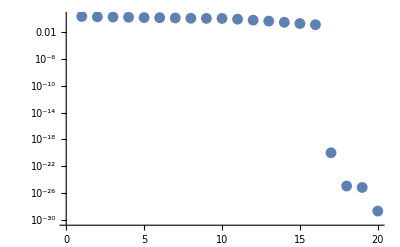

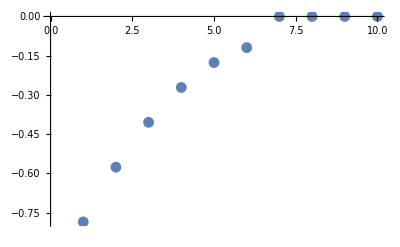

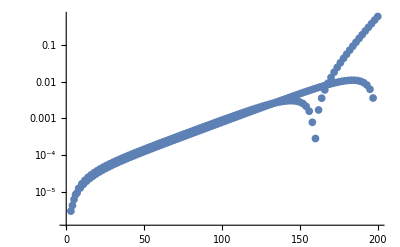

```mathematica
(*Subscript[λ, Ω]=t1,a=s1,b=b1,Subscript[λ, ω]=Ea,s2 Coefficient of \nabla^2 in Eq 3b. t1,b, and s2 have to be multiplied by 10000=1/\delta x^2 to accurately model the laplacian*)
(*USED HIGH DISSIPATIVE COUPLING s1 and b set dissipative coupling*)
Ntval=1000;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.1;
s1val = 1;s2val =2000.0;(*sets 1/deltax^2, here deltax=0.1*)
t1val = 2000;b1val = 100;λval=0.0;ϵval=0.05;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
ListLogPlot[Abs[Eigenvalues[WF1,-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->50000}]],PlotRange->All]
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
(*ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

{-2.37149-2.48507×10^-16 ⅈ}

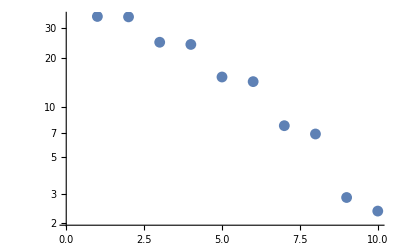

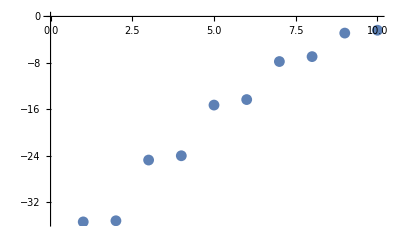

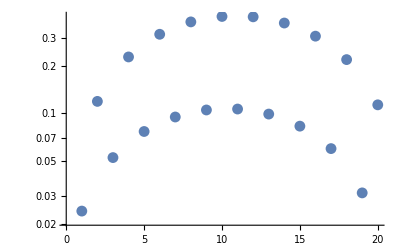

(-41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ | 1.+0. ⅈ | 20.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -1.+0. ⅈ | 20.+0. ⅈ | 2.+0. ⅈ | -41.+0. ⅈ | -1.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 20.+0. ⅈ | 0.+0. ⅈ | -41.+0. ⅈ)

```mathematica
Ntval=10;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=1;
s1val = 1;s2val =20.0;(*sets 1/deltax^2, here deltax=0.1*)
t1val = 20;b1val = 1;λval=0.0;ϵval=0.05;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
ListLogPlot[Abs[Eigenvalues[WF1,-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->50000}]],PlotRange->All]
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
(*ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
MatrixForm[WF1]
```

```mathematica
Eigenvectors[WF1][[2*Ntval-1]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ}

{-0.0977268-1.50684×10^-17 ⅈ}

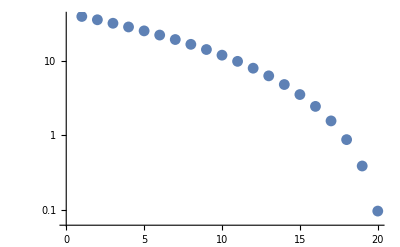

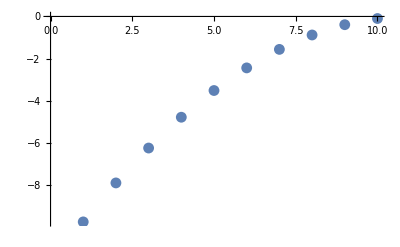

```mathematica
(*Subscript[λ, Ω]=t1,a=s1,b=b1,Subscript[λ, ω]=Ea,s2 Coefficient of \nabla^2 in Eq 3b. t1,Ea, and s2 have to be multiplied by 10000=1/\delta x^2 to accurately model the laplacian*)
(*USED LOW DISSIPATIVE COUPLING s1 and b set dissipative coupling...VALUE OF s1 (a in the Lubensky paper) was lowered*)
Ntval=200;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.001;
s1val = 2;s2val =100.0*4;(*sets 1/deltax^2, here deltax=0.1*)
t1val = 400000*4;b1val = 200*4;λval=0.0;ϵval=0.05;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
ListLogPlot[Abs[Eigenvalues[WF1,-20,Method->{"Arnoldi","Criteria"->"Magnitude"}]],PlotRange->All]
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
(*ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

{-0.0982206-2.87267×10^-15 ⅈ}

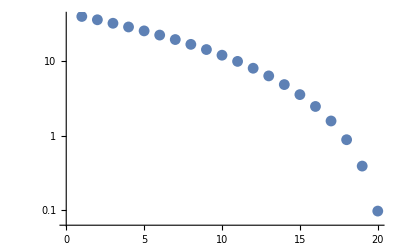

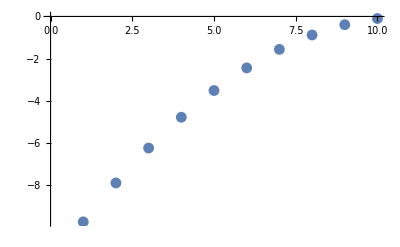

```mathematica
(*Subscript[λ, Ω]=t1,a=s1,b=b1,Subscript[λ, ω]=Ea,s2 Coefficient of \nabla^2 in Eq 3b. t1,Ea, and s2 have to be multiplied by 10000=1/\delta x^2 to accurately model the laplacian*)
(*USED LOW DISSIPATIVE COUPLING s1 and b set dissipative coupling...VALUE OF b1 (b in the Lubensky paper) was lowered*)
Ntval=200;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.001;
s1val = 200;s2val =100.0*4;(*sets 1/deltax^2, here deltax=0.1*)
t1val = 400000*4;b1val = 1*4;λval=0.0;ϵval=0.05;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
ListLogPlot[Abs[Eigenvalues[WF1,-20,Method->{"Arnoldi","Criteria"->"Magnitude"}]],PlotRange->All]
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
(*ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

{-1.00977}

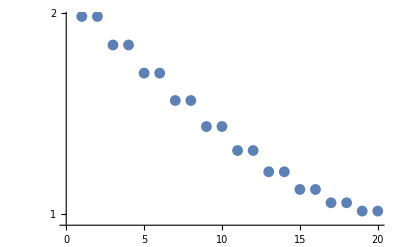

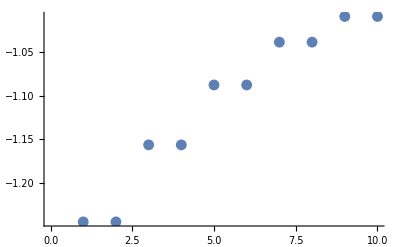

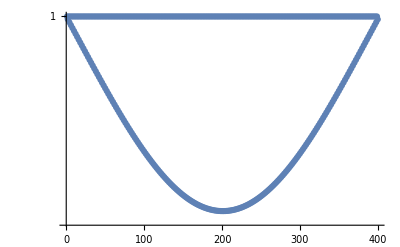

```mathematica
(*Subscript[λ, Ω]=t1,a=s1,b=b1,Subscript[λ, ω]=Ea,s2 Coefficient of \nabla^2 in Eq 3b. t1,b, and s2 have to be multiplied by 10000=1/\delta x^2 to accurately model the laplacian*)
(*USED HIGH DISSIPATIVE COUPLING s1 and b set dissipative coupling*)
(*here beff=1000*800 s2eff=400*1000 a=200. ab/λ^2=200*1000*800/1600 000 >>1 *)
Ntval=800;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=1;
s1val = 0;s2val =10*4;(*sets 1/deltax^2, here deltax=0.1*)
t1val = 10*4;b1val = 0;λval=0.0;ϵval=0.05;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
ListLogPlot[Abs[Eigenvalues[WF1,-20,Method->{"Arnoldi","Criteria"->"Magnitude"}]],PlotRange->All]
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
ListLogPlot[1-Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]
```

```mathematica
(*IGNORE THE CODE BELOW THIS LINE ...........*)
```

```mathematica
WperiodicRot[t1_,a_,Ea_,b_,s2_,q_,k_]:={{-1-2a+2a*Cos[2k+ⅈ q],a},{-2*b+2*b*Cos[2*k+ⅈ q],-2s2+2s2*Cos[2k+ⅈ q]-Ea}}
```

```mathematica
WindingRot1[t1_,a_,Ea_,b_,s2_,q_]:=Table[{Re[Det[Conjugate[WperiodicRot[t1,a,Ea,b,s2,q,k]]]],Im[Det[Conjugate[WperiodicRot[t1,a,Ea,b,s2,q,k]]]]},{k,-π,π,0.001}]
WindingRot2[t1_,a_,Ea_,b_,s2_,q_]:=Table[{k/(2*π),Im[Log[Det[Conjugate[WperiodicRot[t1,a,Ea,b,s2,q,k]]]]]},{k,-π,π,0.01}]
WindingRot3[t1_,a_,Ea_,b_,s2_,q_]:=Table[{k,Re[Det[Conjugate[WperiodicRot[t1,a,Ea,b,s2,q,k]]]]},{k,0,π,0.001}]
WindingRot4[t1_,a_,Ea_,b_,s2_,q_]:=Table[{k,Im[Det[Conjugate[WperiodicRot[t1,a,Ea,b,s2,q,k]]]]},{k,-π,π,0.001}]
```

```mathematica
(*a plays the role of s1*)
```

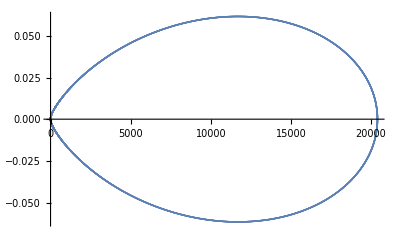

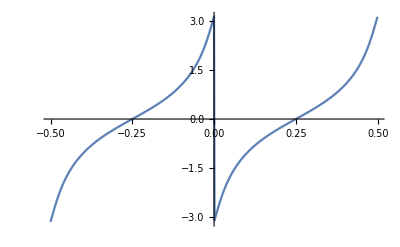

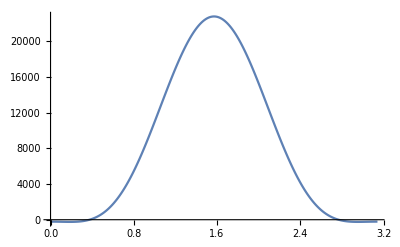

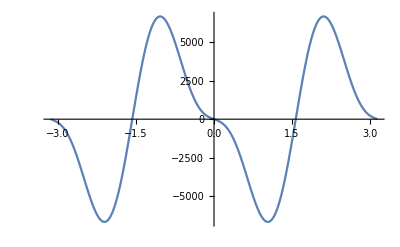

```mathematica
ListPlot[WindingRot1[10000,10,0.001,100,100,0.000005]]
ListPlot[WindingRot2[10000,10,0.001,100,100,0.5],PlotRange->All,Joined->True]
ListPlot[WindingRot3[10000,10,0.001,100,100,0.5],Joined->True,PlotRange->All]
ListPlot[WindingRot4[10000,10,0.001,100,100,0.5],PlotRange->All,Joined->True]
```

```mathematica
WperiodicRot[1000,0.001,0.001,0.1,100,0]
```

{{-1.,0.001},{0.,-0.001}}

```mathematica
Eigenvalues[WperiodicRot[1000,0.001,0.001,0.1,100,0]]
```

{-1.,-0.001}

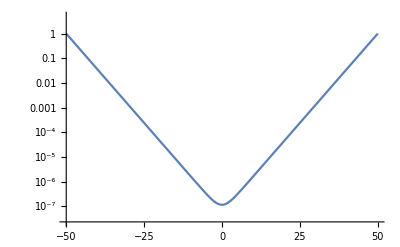

```mathematica
LogPlot[Sech[100/6]Cosh[x/3],{x,-50,50}]
```

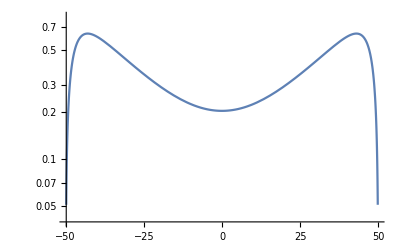

```mathematica
LogPlot[Sech[100/44]Cosh[x/22]-Sech[100/6]Cosh[x/3],{x,-50,50}]
```